First, we initialise the box with the initial colouring, with 1’s on the diamond. The side length (n) can only be an odd multiple of 3 if want a symmetric diamond. We initialise the four different quadrants separately and then stitch them together.

```mathematica
(* n = side length can be an odd multiple of 3 to achieve a symmetric diamond *)
grid4[n_] := grid4[n] = Block[{half = (n + 1) / 2},
(* TODO: rewrite function with Which *)
topLeft = Table[If[i + j < half, Mod[i + j, 3],  Mod[i + j + 1 - half, 2] + 1],{i,0,half- 1},{j,0,half - 1}];
topRight = Table[If[j - i >=  half, Mod[j - i  - half - 1 , 3], Mod[i + j + 1 - half, 2] + 1],{i,0,half- 1},{j,half,n - 1}];
bottomLeft = Table[If[i - j >=  half, Mod[- j + i  + half + 1 , 3], Mod[i + j + 1 - half, 2] + 1],{i, half, n - 1},{j, 0, half - 1}];
bottomRight = Table[If[i + j > 3 half - 3, Mod[- i - j + 1, 3],  Mod[i + j + 1 - half, 2] + 1],{i,half,n - 1},{j,half,n - 1}];

top = Join[topLeft[[#]], topRight[[#]]] & /@ Range[Length[topLeft]];
bottom = Join[bottomLeft[[#]], bottomRight[[#]]] & /@ Range[Length[bottomLeft]];

finalTable = Join[top, bottom]
]
```

The below box shows the initial colouring for any valid n up to 237.

```mathematica
{ColorSlider[Dynamic[colour0]], Dynamic[colour0]}
{ColorSlider[Dynamic[colour1]], Dynamic[colour1]}
{ColorSlider[Dynamic[colour2]], Dynamic[colour2]}
colourRules={0->Red,1->Yellow,2->Blue};
dynamicColourRules={0->colour0,1->colour1,2->colour2};
Manipulate[ArrayPlot[grid4[3(2k - 1)],ColorRules->dynamicColourRules,Frame->True],{k,1,40,1}]
```

{$CellContext`colour0,}

{$CellContext`colour1,}

{$CellContext`colour2,}

Now, pick a random cell. If the colour of the cell can be changed, then do so with 50% probability.

```mathematica
moreSteps = 450000000;
{time, finalGrid} = viewAfterSteps[n, grid3[n], moreSteps];
ArrayPlot[finalGrid, ColorRules->colorRules,Frame->True]
time
```

```mathematica
selectRandomCell[n_] := RandomChoice[Tuples[Range[2, n - 1], 2]];
coinFlip[] := RandomChoice[{True, False}]
changeColour[grid_, pos_, newVal_] := ReplacePart[grid, pos -> newVal]

(* checkChange returns -1 if the colour in grid at pos cannot be flipped, otherwise it returns the possible colour to which pos can be changed *)
checkChange[n_, pos_, grid_] := Module[{x, remValues},
	If[Length[x = Intersection[
		grid[[DeleteDuplicates[Clip[pos[[1]] + {-1, 1}, {1,n}]], pos[[2]]]] ~ Join ~ grid[[pos[[1]], DeleteDuplicates[Clip[pos[[2]] + {-1, 1}, {1,n}]]]], 
		remValues = DeleteCases[{0,1,2}, grid[[Sequence @@ pos]]]]] > 1, -1, DeleteCases[remValues, x[[1]]][[1]]]
	]
	
(*randomChange[n_, steps_, grid_] := NestList[Catch[If[checkChange[n, selectRandomCell[n], #] >= 0, Throw[changeColour[#, pos, checkChange[n, selectRandomCell[n], #]]], Throw[#]]] &, grid, steps]*)
randomChange2[n_, grid_] := If[x = checkChange[n, pos = selectRandomCell[n], grid] >= 0 && coinFlip[], changeColour[grid, pos, checkChange[n, pos, grid]], grid]
viewChangeSteps[n_, grid_, steps_] := (gridList = NestList[randomChange2[n, #] &, grid, steps]; Manipulate[ArrayPlot[gridList[[k]],ColorRules->colorRules,Frame->True],{k,1,steps,1}])
viewAfterSteps[n_, initialGrid_, steps_, logInterval_, prevStep_] := Module[{step = 0},
  PrintTemporary[ProgressIndicator[Dynamic[step/steps]]]; {time, finalGrid} = AbsoluteTiming[Nest[(If[Mod[step, logInterval] == 0, Export[StringJoin[ToString[NotebookDirectory[]], "output files/log_", ToString[step + prevStep], ".mx"], #]]; step++; randomChange2[n, #]) &, initialGrid, steps + 1]]]
displayTime[time_] := DateString[time, {"Hour", ":", "Minute", ":", "Second"}]
```

```mathematica
n = 99;
steps = 10000000;
viewChangeSteps[n, grid4[n], steps]
```

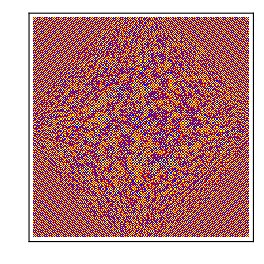

07:24:54

```mathematica
n = 273;
steps = 350000000;
moreSteps = 350000000;
logInterval = 10000000;
{time, finalGrid} = viewAfterSteps[n, grid4[n], moreSteps, logInterval];
ArrayPlot[finalGrid, ColorRules->colorRules,Frame->True]
displayTime[time]
```

```mathematica
time3
```

74796.2

```mathematica
n = 273;
newSteps = 1000000000;
logInterval = 10000000;
{time4, finalGrid4} = viewAfterSteps[n, finalGrid2, newSteps, logInterval, 1000000000];
```

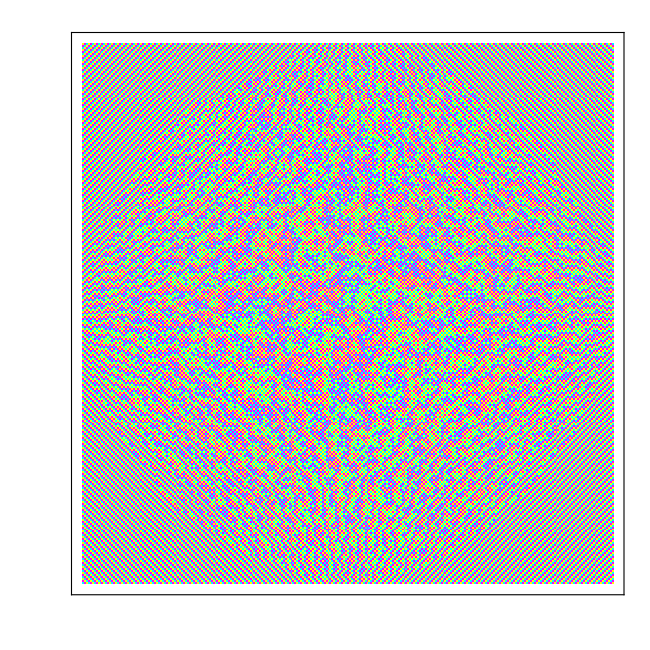

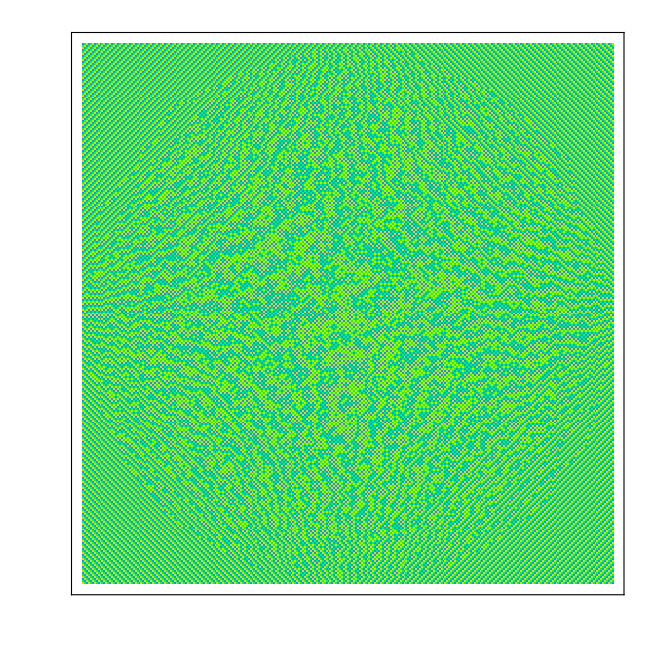

```mathematica
colorRules={0->Yellow,1->Magenta,2->Cyan};
finalGrid4 = Import[NotebookDirectory[], "output files/log_600000000.mx"];
ArrayPlot[finalGrid4, ColorRules->colorRules,Frame->True]
colorRules={0->Orange,1->Purple,2->RGBColor[#00FF00]};
finalGrid4 = Import[NotebookDirectory[], "output files/log_1240000000.mx"];
ArrayPlot[finalGrid4, ColorRules->dynamicColourRules,Frame->True]
```

```mathematica
newSteps = 1000000000;
logInterval = 10000000;
{time5, finalGrid5} = viewAfterSteps[n, finalGrid4, newSteps, logInterval, 1240000000];
displayTime[time5]
ArrayPlot[finalGrid5, ColorRules->colourRules,Frame->True]
```

21:12:55

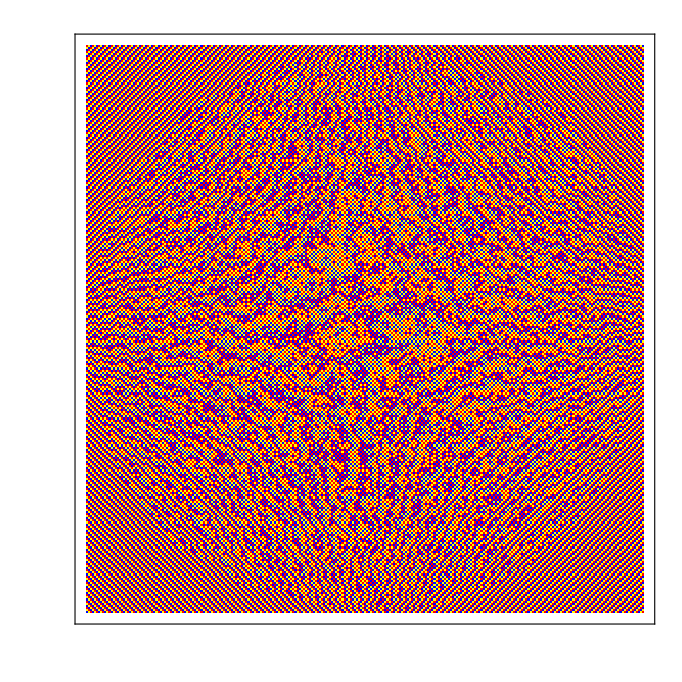

```mathematica
Manipulate[ArrayPlot[grid3[3(2k - 1)],ColorRules->colorRules,Frame->True],{k,1,40,1}]
Import[NotebookDirectory]
```

```mathematica
(* Test checkChange() *)
n = 9
MatrixForm[grid = grid3[n]]
(*pos = select[9]*)
pos = selectRandomCell[n]
checkChange[n, pos, grid3[n]]
```

9

(0 | 1 | 2 | 0 | 1 | 2 | 0 | 1 | 2
1 | 2 | 0 | 1 | 2 | 1 | 2 | 0 | 1
2 | 0 | 1 | 2 | 1 | 2 | 1 | 2 | 0
0 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 2
1 | 2 | 1 | 2 | 1 | 2 | 1 | 2 | 1
2 | 1 | 2 | 1 | 2 | 1 | 2 | 1 | 0
1 | 2 | 1 | 2 | 1 | 2 | 1 | 0 | 2
0 | 1 | 2 | 1 | 2 | 1 | 0 | 2 | 1
2 | 0 | 1 | 2 | 1 | 0 | 2 | 1 | 0)

{8,7}

-1

```mathematica
Animate[ColorSlider[Pink, 
  ImageSize -> {150 + 50 Cos[t], 40 + 10 Sin[t]}], {t, 2 π, 0}, 
 AnimationRate -> 1, AnimationRunning -> False]
```

```mathematica
{ColorSlider[Dynamic[x]], Dynamic[x]}
```

{$CellContext`x,}

```mathematica
x
```

RGBColor[0.3764705882352941, 0., 1.]